BookChapterNumber

Symmetry Breaking in Phase Transition

## Concrete Example: Van der Waals Theory

### Subsection. Review: Ideal Gas

#### Free Energy

The free energy of ideal gas is easy to derive. We first write down its canonical partition function:

Z=∑exp(-β E)=1/(N!)(∑_k exp(-β ϵ_k))^N

Here ϵ_k=ℏ^2 k^2/2m is the energy of a single particle, and the 1/N! factor is due to the indistinguishability of particles.

⟶^(continuous k)1/(N!)(∫(ⅆ^3 xⅆ^3 k)/(2π)^3 exp(-β (ℏ^2 k^2)/(2m)))^N=1/(N!)(V/λ^3)^N

where we introduced the thermal wavelength λ≡√(2π β ℏ^2/m). Then

F=-T ln Z=T ln N!-N T ln V/λ^3
≃T(N ln N-N)-N T ln V/λ^3=-N T-N T ln V/(N λ^3)

#### Equation of State

The pressure is found from the free energy

P=-((∂F)/(∂V))_T=(N T)/V

or

P V=N T

### Subsection. Free Energy of Van der Waals Gas

The free energy of van der Waals gas can be obtained by simple modifications to the ideal gas:

F=-N T-N T ln (V-N b)/(N λ^3)-(a N^2)/V

The equation of state is

P=-((∂F)/(∂V))_T=(N T)/(V-N b)-(a N^2)/V^2

or

(P v^2+a)(v-b)=v^2 T

where v≡V/N.

### Subsection. Liquid-Gas Transition

The van der Waals gas is able to undergo a liquid-gas phase transition.

-Graphics-

We know that the system is stable when

((∂P)/(∂V))_T<0

Thus the states denoted by the dashed line does not actually occur, which means that a discontinuous phase transition will happen. During this transition,

((∂P)/(∂V))_T=0

i.e. the pressure will be constant.

#### Condition for Two-Phase Coexistence

The variation of entropy of a two-phase system is

δ S=δ S_1+δ S_2
=(1/T_1 δ E_1+P_1/T_1 δ V_1-μ_1/T_1 δ N_1)+(1/T_2 δ E_2+P_2/T_2 δ V_2-μ_2/T_2 δ N_1)

But due to conservation of energy, volume and particle numbers, in equilibrium

δ E_1+δ E_2=0, δ V_1+δ V_2=0, δ N_1+δ N_2=0

Thus

δ S=δ S_1+δ S_2
=(1/T_1-1/T_2)δ E_1+(P_1/T_1-P_2/T_2)δ V_1-(μ_1/T_1-μ_2/T_2)δ N_1

This should be 0 in equilibrium. Thus we obtain the conditions

T_1=T_2, P_1=P_2, μ_1=μ_2

#### Equal-Area Law

On the P-V graph, the condition μ_1=μ_2 can be expressed as

μ_2-μ_1=∫_1^2 ⅆμ

But we know that μ is G of the whole system (with fixed N=N_1+N_2) per particle. Thus

ⅆμ=1/N ⅆG=-S/NⅆT+vⅆP ⟶^(fixed T) vⅆP

⟹∫_1^2 v ⅆP=0

### Subsection. The Critical Point

The critical point is determined by the condition

(∂P)/(∂V)=(∂^2 P)/(∂V^2)=0

which gives

T_c=(8a)/(27b),    V_c=3N b,    P_c=a/(27 b^2)

```mathematica
Clear["Global`*"]
P[V_]:=(𝒩 T)/(V-𝒩 b)-(a 𝒩^2)/V^2;
deri1=D[P[V],V]; 
deri2=D[P[V],{V,2}];
rep=Solve[deri1==0&&deri2==0,{T,V}][[1]]//Simplify;
{Tc,Vc,Pc}={T,V,P[V]}/.rep
```

{(8 a)/(27 b),3 b 𝒩,a/(27 b^2)}

We rewrite the equation of state in terms of dimensionless variables

T/T_c→T, V/V_c→V, P/P_c→P

⟹ P=(8T)/(3V-1)-3/V^2

```mathematica
P[V]/Pc/.{T->T Tc,V->V Vc}//Simplify
```

(3-9 V+8 T V^2)/(V^2 (-1+3 V))

Then, to study the deviation from the critical point, we introduce the variables

p=P-1, w=V-1, t=T-1

The critical point is still determined by

(∂p)/(∂w)=0, (∂^2 v)/(∂w^2)=0

In particular, w measures the deviation from the critical volume (per particle) or density. It is called the order parameter, which characterizes the phase transition.

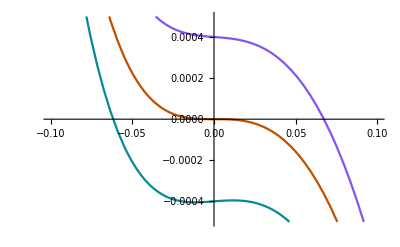

```mathematica
p[t_,w_]:=P[V]/Pc-1/.{T->T Tc,V->V Vc}//.{V->1+w,T->1+t}//Simplify
pPlots=Table[p[t,w],{t,-10^-4,10^-4,10^-4}];
Plot[pPlots,{w,-0.1,0.1},PlotRange->{Automatic,{-5*10^-4,5*10^-4}}]
```

Expand p as a series of t,w, we obtain

p=4t-6t w-3/2 w^3+higher order terms

```mathematica
a=-3;B=-3/8;
a/(2B)
```

4

```mathematica
Series[p[t,w],{t,0,1},{w,0,3}]//Simplify
```

(-(3 w^3)/2+O[w]^4)+(4-6 w+9 w^2-(27 w^3)/2+O[w]^4) t+O[t]^2

Note: although there is a term 9t w^2, we do not include it in the expansion. This is because we shall later find out that w∝(|t|)^(1/2) (see below), and then the t w^2∝(|t|)^2 term is of higher order than w^3∝(|t|)^(3/2).

The phase transition is determined by the equal-area law

∫_1^2 vⅆP=0 ⟹ ∫_1^2 wⅆp=0

⟹∫_w_1^w_2 w (∂p)/(∂w)ⅆw≃∫_w_1^w_2 w ∂/(∂w)(4t-6t w-3/2 w^3)ⅆw
	=3/8(w_1^2-w_2^2)(8t+3(w_1^2+w_2^2))=0

Thus w_1=-w_2≡w. Then

p_1=p_2 ⟹ -6t w-3/2 w^3=6t w+3/2 w^3

⟹w=√(2(-t))

This is the dependence of the order parameter on the temperature near the critical point.

## Symmetry Breaking in Phase Transition

### Subsection. Symmetry Breaking in the van der Waals Theory

To illustrate the symmetry breaking, we separate a system of van der Waals gas  (2N particles, total volume 2V) into two parts 1 and 2 by some wall. The wall allows exchange of heat, so the two parts will finally reach equilibrium with the same temperature, but they may be in different phases, characterized by the difference in specific volume (or densities).

Therefore, we define the difference between specific volume as the order parameter describing the phase transition:

w≡(v_1-v_2)/v

Consider the following two cases:

#### a. Fixed N_1,N_2=N; Variable V_1,V_2

This is done by a movable and impenetrable wall. The free energy density of the whole system (as function of N_1 and T) is

F_tot(V_1,T)=F(N,V_1,T)+F(N,2V-V_1,T)

We want write F_tot as a function of w instead of V_1. Using

v_1=V_1/N, v_2=V_2/N=(2V-V_1)/N, v=(2V)/(2N)=V/N

we find the relation between w and V_1:

w=2(V_1/V-1)   ⟹   V_1=(1+w/2)V

Then

F(w,T)=-2N T-(2a N^2)/(V(1-w^2))-N T ln

```mathematica
Clear["Global`*"]
F[𝒩_,V_,T_]:=-𝒩 T-𝒩 T Log[(V-𝒩 b)/(𝒩 λ^3)]-(a 𝒩^2)/V
```

```mathematica
rep=Solve[V1/𝒩==(1+w)V/𝒩,V1][[1]]
```

{V1→V (1+w)}

```mathematica
(* free energy at critical v *)
f=FullSimplify[(F[𝒩,V1,T]+F[𝒩,2V-V1,T])//.rep//.{V->3b 𝒩,a->(27b Tc)/8}];
fapprox=Normal[Series[f,{w,0,5}]//Simplify]
```

9/4 (T-Tc) w^2 𝒩+9/32 (9 T-8 Tc) w^4 𝒩-1/4 𝒩 (8 T+9 Tc+8 T Log[(2 b)/λ^3])

```mathematica
fderi=D[fapprox,w];
wlist=Simplify[Solve[fderi==0,w]]/.Rule->List;
wlist=wlist[[All,1,2]]
```

{0,-(2 √(-T+Tc))/(√(9 T-8 Tc)),(2 √(-T+Tc))/(√(9 T-8 Tc))}

```mathematica
Series[Simplify[wlist[[3]]//.{T->(1-t) Tc},Tc>0],{t,0,2}]
```

2 √t+9 t^(3/2)+O[t]^(5/2)

#### b. Variable N_1,N_2; Fixed V_1,V_2=V

This is done by a fixed and penetrable wall. The total free energy (as function of N_1 and T) is

F_tot(N_1,T)=F_1(N_1,V,T)+F_2(2N-N_1,V,T)

w≡(v_1-v_2)/v

We want write F_tot as a function of w instead of V_1. Using

v_1=V/N_1, v_2=V/N_2=V/(2N-N_1), v=(2V)/(2N)=V/N

we find the relation between w and N_1:

w=(2N(N-N_1))/(N_1(2N-N_1))   ⟹   N_1=(1+w±√(1+w^2))/w N

Since 0≤N_1≤2N, the physical solution should take negative sign:

N_1=(1+w-√(1+w^2))/w N

```mathematica
rep=Simplify[Solve[w==(V/𝒩1-V/(2𝒩-𝒩1))/(V/𝒩),𝒩1],𝒩>0][[1]]
```

{𝒩1→((1+w-√(1+w^2)) 𝒩)/w}

```mathematica
(* free energy at critical v *)
f=FullSimplify[(F[𝒩1,V,T]+F[2𝒩-𝒩1,V,T])//.rep//.{V->3b 𝒩,a->(27b Tc)/8}];
fapprox=Normal[Series[f,{w,0,5}]//Simplify]
```

9/16 (T-Tc) w^2 𝒩-9/512 (15 T-16 Tc) w^4 𝒩-1/4 𝒩 (8 T+9 Tc+8 T Log[(2 b)/λ^3])

```mathematica
fderi=D[fapprox,w];
wlist=Simplify[Solve[fderi==0,w],0<T<Tc]/.Rule->List;
wlist=wlist[[All,1,2]]
```

{0,-4 √((T-Tc)/(15 T-16 Tc)),4 √((T-Tc)/(15 T-16 Tc))}

```mathematica
Series[Simplify[4 √((-(T-Tc))/(-(15 T-16 Tc)))//.{T->(1-t) Tc},Tc>0],{t,0,2}]
```

4 √t-30 t^(3/2)+O[t]^(5/2)

### Subsection. Landau Theory of Symmetry Breaking

#### Critical Exponents

Define t≡(T-T_c)/T_c. We have the following 8 critical exponents near the phase transition point:

Specific heat: C_P∝(|t|)^-α,C_P∝h^-ϵ

Order parameter: m∝(-t)^β, m∝h^(1/δ)

Susceptibility: χ∝(|t|)^-γ, γ>0

Correlation length: ξ∝(|t|)^-ν, ξ∝h^-μ (ν,μ>0)

Correlation funtion: Γ(r)∝r^(-(d-2+ζ))

Here d is the spatial dimension, and h is the field coupling to the order parameter.

We shall see below that the Landau theory gives

α=0, β=1/2, γ=1, δ=3
ϵ=0, μ=1/3, ν=1/2, ζ=0

#### Second Order Phase Transitions

For a system where second order phase transition (with order parameter m) can occur at temperature T_c due to symmetry breaking, the Gibbs free energy (assuming that the phase transition happens under constant T) is of the form (omitting the pressure variable)

G(T,m)=a(T)+1/2 b(T)m^2+1/4 c(T)m^4+...

The numerical factors 1/2,1/4 etc are introduced for convenience.

We may also add the coupling to an external field h:

G(T,m,h)=-h m+a(T)+1/2 b(T)m^2+1/4 c(T)m^4+...

Near the critical temperature T_c, the functions b,c have the property (assume that the symmetrical phase corresponds to T>T_c)

b(T)=b_0(T-T_c), b_0>0

c(T)>0

Now we calculate the various critical exponents.

##### Order Parameter

The order parameter is determined by

(∂G)/(∂m)=-h+b_0(T-T_c)m+c(T)m^3=0

m∝(-t)^β:

Setting h=0, when T<T_c, we have nonzero solutions of m:

b_0(T-T_c)m+c(T)m^3=0

⟹m=±√((b_0(T_c-T))/c)∝(-t)^(1/2)

Thus β=1/2.

m∝h^(1/δ):

Setting T=T_c:

-h+c(T_c)m^3=0 ⟹ m=(h/(c(T_c)))^(1/3)∝h^(1/3)

Thus δ=3.

##### Specific Heat

C_P=(T((∂S)/(∂T)))_P=-T (∂^2 G)/(∂T^2)

```mathematica
Clear["Global`*"]
G=-h m[T]+a[T]+1/2 b0(T-Tc)m[T]^2+1/4 c[T] m[T]^4;
Cp=FullSimplify[-T D[G,{T,2}]];
```

C_P∝(|t|)^-α:

Set h=0. When T>T_c, m≡0 and we obtain

```mathematica
m[T_]:=0
Simplify[Cp/.{h->0}]
```

-T a''[T]

C_P=-T(ⅆ^2 a(T))/(ⅆ T^2) ⟹ α_+=0

When T<T_c, substituting in m^2=b_0(T_c-T)/c, we obtain

```mathematica
m[T_]:=√(b0(Tc-T)/c[T])
Simplify[Cp/.{h->0},{T<Tc}]/.{T->Tc}//Simplify
```

(b0^2 Tc)/(2 c[Tc])-Tc a''[Tc]

C_P→-T_c(ⅆ^2 a(T_c))/(ⅆ T^2)+(T_c b_0^2)/(2c(T_c)) ⟹ α_-=0

##### Susceptibility

χ∝(|t|)^-γ

By definition

χ≡[(∂m)/(∂h)]_(h=0)

Taking h-derivatives of the equation ∂G/∂m=0, we have

-1+(b_0 T_c t+3c(T)m^2)(∂m)/(∂h)=0

⟹ (∂m)/(∂h)=1/(b_0 T_c t+3c(T)m^2)

But we know that m∝(-t)^(1/2), therefore, regardless of whether t>0, we have

(∂m)/(∂h)∝(|t|)^-1 ⟹ γ=1

#### First Order Phase Transitions

G(T,m)=a(T)+1/2 b(T)m^2-1/3 c(T)m^3+1/4 d(T)m^4